# CARBAPENEM RESISTANCE MODEL

## Data

### Preparing Directory

Clear all variables. Set directory and change setting such that when it closes it closes all outputs.

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndExecute[FrontEndToken["DeleteGeneratedCells"]]}];
```

### Load Data

Reading country data on consumption and resistance and assigning them to appropriate variables.

```mathematica
countryname="US_DDD"; 
data=Import["DataSheet_cddep.xlsx",{"Data",countryname}];
data = data[[All,2;;]];
years = data[[1]];
tt = Length[years]; 
nop = (Length[data]-5)/2; (*# of pathogens*)
isolates = data[[2;;Length[data]-4;;2]];
resistance = data[[3;;Length[data]-4;;2]];
rfreq =resistance/isolates;
carbcons =  data[[-1]];
conbreak = data[[-3,1;;nop]]; (*CBP consumption for KP, PA, AB*)
cbp =data[[-2,1]]*Table[carbcons*conbreak[[i]],{i,1,nop}];
```

## Model

### Parameters & Model Structure

r(t) = frequency of resistance
k_s= natural growth rate of the sensitive strain
k_r= natural growth rate of the resistance strain (k_r < k_s)
θ = k_r-k_s< 0 
a = CBP consumption (DDD)

```mathematica
r[t_,r0_,ks_,θ_]:=ⅇ^(Total[ks*a[[1;;t]]]+θ*t)/((1/r0)-1+ⅇ^(Total[ks*a[[1;;t]]]+ θ*t));
```

### Likelihood

```mathematica
Lik[r0_,ks_,θ_]:= Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,ks,θ]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,ks,θ]],{j,1,tt}]]
```

### Model Fitting

```mathematica
max  = PadRight[{},nop,Null];
fr0 = max; fks=max; fθ=max;
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],a = cbp[[i]],{max[[i]],{fr0[[i]],fks[[i]],fθ[[i]]}}=NMaximize[{Lik[r0,ks,θ],0<r0<1,θ<-0.1},{r0,ks,θ}, MaxIterations->100000]}]

fr0 = Table[fr0[[i]][[2]],{i,1,nop}];
fks = Table[fks[[i]][[2]],{i,1,nop}] ;
fθ=Table[fθ[[i]][[2]],{i,1,nop}];

(*create table of fitted values*)
params= Join[{max},{fr0},{fks},{fθ}];
headings1=Prepend[params,{"KP","PA","AB","EA/C"}];
headings2=MapThread[Prepend,{headings1,{"","Likelihood","r0","k_s","θ"}}];
Grid[headings2,Frame-> All]
```

| KP | PA | AB | EA/C
Likelihood | -338.471 | -120.611 | -160.27 | -113.668
r0 | 0.00618336 | 0.187208 | 0.171297 | 0.000773001
k_s | 841.498 | 181.436 | 952.634 | 1672.68
θ | -0.1 | -0.1 | -0.1 | -0.1

#### Plots

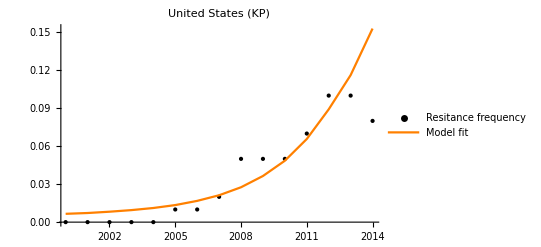

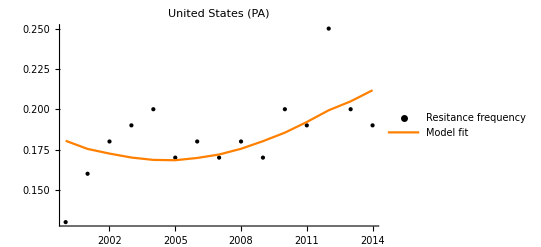

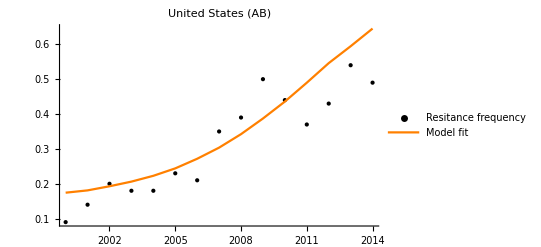

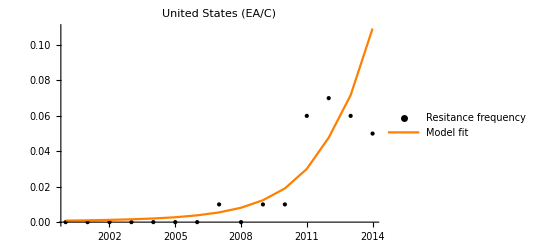

```mathematica
t=Range[1,tt]; 
res = Table[Transpose@{years,rfreq[[i]]},{i,1,nop}]; (*resistance frequency data*)
x  = PadRight[{},nop,Null];
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],a = cbp[[i]],x[[i]] = Table[r[j,fr0[[i]],fks[[i]],fθ[[i]]],{j,1,tt}]}];
fit =  Table[Transpose@{years,x[[i]]},{i,1,nop}];

plotD = Table[ListPlot[{res[[i]]},PlotStyle->{{Black,PointSize[Large]}},PlotRange->All,PlotLegends->{"Resitance frequency"}],{i,1,nop}];
plotM = Table[ListLinePlot[{fit[[i]]},PlotStyle->{{Orange,Thick}},AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States",PlotLegends->{"Model fit"}],{i,1,nop}];
Show[plotD[[1]],plotM[[1]],PlotRange->All,PlotLabel->"United States (KP)"] 
Show[plotD[[2]],plotM[[2]],PlotRange->All,PlotLabel->"United States (PA)"]
Show[plotD[[3]],plotM[[3]],PlotRange->All,PlotLabel->"United States (AB)"]
Show[plotD[[4]],plotM[[4]],PlotRange->All,PlotLabel->"United States (EA/C)"]
```

## Projections

### Status Quo & Interventions

```mathematica
cbp0 = data[[-2,1]]*carbcons[[-1]];  (*current CBP consumption*)
ti=years[[-1]]; (*projectsion begin at year Subscript[t, i]*)
tf =2030; (*projection until year Subscript[t, f]*) 
nyears = tf -ti; (*# of years to project across*)
pyears = Range[ years[[-1]],tf];
```

```mathematica
(*Status Quo: maintain current CBP consumption*)
projSQ =ConstantArray[cbp0,Round[nyears]]; 
cbpSQ = Table[Join[cbp,projSQ]*conbreak[[i]],{i,1,nop}];
```

```mathematica
(*Interventions:
(0) sparing1: 0 consumption at Subscript[t, i]
(1) sparing2: linear reduction to 0 consumption by Subscript[t, f]
(2) stewardship1: immediate reduction to a % of current consumption
(3) stewardship2: linear reduction to the a % of current consumption *) 

intv = 0.4; (*reduce current carbapenem consumption by (1-intv) % in next npy years linearly*)

option = 3; (*select 0-3; see above*)
If[option==0, projI = ConstantArray[0,Round[nyears]], 
If[option==1,projI = Range[cbp0,0,(-1)*cbp0/(nyears-1)], 
If[option==2, projI=ConstantArray[intv*cbp0,Round[nyears]], 
If[option == 3, projI = Range[cbp0,intv*cbp0,cbp0*(intv-1)/(nyears-1)]]]]];
cbpI = Table[Join[cbp, projI]*conbreak[[i]],{i,1,nop}];
```

```mathematica
(*Status Quo resistance frequency*)
y  = PadRight[{},nop,Null];
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],a = cbpSQ[[i]],y[[i]] = Table[r[j,fr0[[i]],fks[[i]],fθ[[i]]],{j,tt,tt+nyears}]}];
rSQ =  Table[Transpose@{pyears,y[[i]]},{i,1,nop}];

(*Intervention resistance frequency*)
z  = PadRight[{},nop,Null];
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],a = cbpI[[i]],z[[i]] = Table[r[j,fr0[[i]],fks[[i]],fθ[[i]]],{j,tt,tt+nyears}]}];
rI =  Table[Transpose@{pyears,z[[i]]},{i,1,nop}];
```

Part::take: Cannot take positions 1 through 21 in {{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},«18»,0.000496251}.

Part::take: Cannot take positions 1 through 22 in {{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},«18»,0.000496251}.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 21 in {{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},«18»,0.0001985}.

Part::take: Cannot take positions 1 through 22 in {{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},«18»,0.0001985}.

General::stop: Further output of Part::take will be suppressed during this calculation.

### Projection Plots

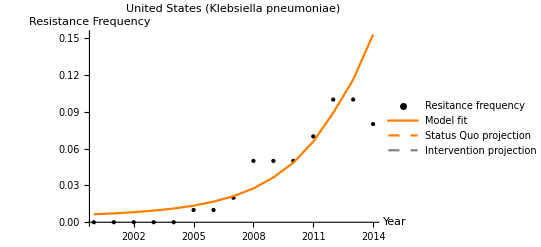

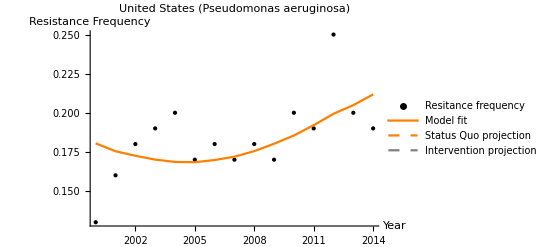

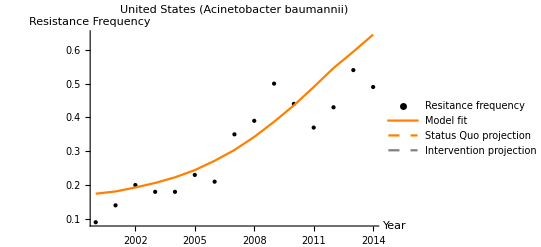

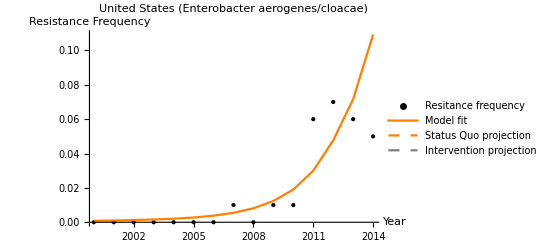

```mathematica
plotPSQ = Table[ListLinePlot[{rSQ[[i]]},PlotStyle->{{Orange,Thick,Dashed}},PlotStyle->Gray,AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States",PlotLegends->{"Status Quo projection"}],{i,1,nop}];
plotPI = Table[ListLinePlot[{rI[[i]]},PlotStyle->{{Gray,Thick,Dashed}},AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States",PlotLegends->{"Intervention projection"}],{i,1,nop}];
Show[plotD[[1]],plotM[[1]],plotPSQ[[1]],plotPI[[1]],PlotRange->All,PlotLabel->"United States (Klebsiella pneumoniae)",AxesLabel->{"Year","Resistance Frequency"}] 
Show[plotD[[2]],plotM[[2]],plotPSQ[[2]],plotPI[[2]],PlotRange->All,PlotLabel->"United States (Pseudomonas aeruginosa)",AxesLabel->{"Year","Resistance Frequency"}]
Show[plotD[[3]],plotM[[3]],plotPSQ[[3]],plotPI[[3]],PlotRange->All,PlotLabel->"United States (Acinetobacter baumannii)",AxesLabel->{"Year","Resistance Frequency"}]
Show[plotD[[4]],plotM[[4]],plotPSQ[[4]],plotPI[[4]],PlotRange->All,PlotLabel->"United States (Enterobacter aerogenes/cloacae)",AxesLabel->{"Year","Resistance Frequency"}]
```

# Economic & Health Outcomes

### Mortality

```mathematica
ipneu=5610000; (*pneumonia incidence*)
ipp=conbreak*ipneu; (*pneumonia incidence by pathogen*)

(*carbapenem prescription breakdown for KPC*)
kp={20/105,19/105,29/105,35/105}; (*carbapenem monotherapy, carbapenem combination therapy, sparing mono, sparing combo*)

(*associated mortality rates*)
rkpm={0.467,0.278,0.467,0.304}; (*carbapenem monotherapy, carbapenem combination therapy, sparing mono, sparing combo*)

(*susceptible mortality rates dummy variables*)
skpm={0.234,0.234,0.234,0.234};
```

```mathematica
(*kp # of deaths*)
kpdeath[r_]:=(Total[kp*rkpm]*r + Total[kp*skpm]*(1-r))*ipp[[1]];
Apply[kpdeath,{z[[1]]}]
```

{{210405.,210533.,210716.,210750.,210838.,210955.,211104.,211174.,211303.,211406.,211451.,211556.,211602.,211433.,211540.},{211353.,211497.,211703.,211741.,211840.,211972.,212139.,212218.,212362.,212477.,212528.,212646.,212697.,212508.,212628.},{212279.,212438.,212665.,212708.,212817.,212963.,213148.,213234.,213394.,213521.,213577.,213707.,213764.,213555.,213687.},{213150.,213323.,213571.,213617.,213736.,213894.,214095.,214190.,214363.,214501.,214562.,214703.,214765.,214538.,214682.},{213934.,214120.,214386.,214435.,214563.,214732.,214948.,215049.,215235.,215383.,215448.,215599.,215665.,215422.,215576.},{214603.,214800.,215080.,215132.,215267.,215446.,215673.,215780.,215976.,216132.,216201.,216360.,216430.,216173.,216336.},885789. ((0.369571 ⅇ^(839.398+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;21⟧))/(160.724+ⅇ^(839.398+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;21⟧))+0.229543 (1-ⅇ^(839.398+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;21⟧)/(160.724+ⅇ^(839.398+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;21⟧)))),885789. ((0.369571 ⅇ^(839.298+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;22⟧))/(160.724+ⅇ^(839.298+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;22⟧))+0.229543 (1-ⅇ^(839.298+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;22⟧)/(160.724+ⅇ^(839.298+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;22⟧)))),885789. ((0.369571 ⅇ^(839.198+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;23⟧))/(160.724+ⅇ^(839.198+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;23⟧))+0.229543 (1-ⅇ^(839.198+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;23⟧)/(160.724+ⅇ^(839.198+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;23⟧)))),885789. ((0.369571 ⅇ^(839.098+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;24⟧))/(160.724+ⅇ^(839.098+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;24⟧))+0.229543 (1-ⅇ^(839.098+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;24⟧)/(160.724+ⅇ^(839.098+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;24⟧)))),885789. ((0.369571 ⅇ^(838.998+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;25⟧))/(160.724+ⅇ^(838.998+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;25⟧))+0.229543 (1-ⅇ^(838.998+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;25⟧)/(160.724+ⅇ^(838.998+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;25⟧)))),885789. ((0.369571 ⅇ^(838.898+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;26⟧))/(160.724+ⅇ^(838.898+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;26⟧))+0.229543 (1-ⅇ^(838.898+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;26⟧)/(160.724+ⅇ^(838.898+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;26⟧)))),885789. ((0.369571 ⅇ^(838.798+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;27⟧))/(160.724+ⅇ^(838.798+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;27⟧))+0.229543 (1-ⅇ^(838.798+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;27⟧)/(160.724+ⅇ^(838.798+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;27⟧)))),885789. ((0.369571 ⅇ^(838.698+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;28⟧))/(160.724+ⅇ^(838.698+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;28⟧))+0.229543 (1-ⅇ^(838.698+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;28⟧)/(160.724+ⅇ^(838.698+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;28⟧)))),885789. ((0.369571 ⅇ^(838.598+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;29⟧))/(160.724+ⅇ^(838.598+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;29⟧))+0.229543 (1-ⅇ^(838.598+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;29⟧)/(160.724+ⅇ^(838.598+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;29⟧)))),885789. ((0.369571 ⅇ^(838.498+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;30⟧))/(160.724+ⅇ^(838.498+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;30⟧))+0.229543 (1-ⅇ^(838.498+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;30⟧)/(160.724+ⅇ^(838.498+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;30⟧)))),885789. ((0.369571 ⅇ^(838.398+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;31⟧))/(160.724+ⅇ^(838.398+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;31⟧))+0.229543 (1-ⅇ^(838.398+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;31⟧)/(160.724+ⅇ^(838.398+{{0.0000303306,0.0000361024,0.0000441684,0.0000456634,0.0000494602,0.0000544562,0.0000607114,0.0000636044,0.0000688786,0.0000730182,0.0000748188,0.0000789826,0.0000807925,0.0000741017,0.0000783554},{0.0000477937,0.0000568886,0.0000695987,0.0000719544,0.0000779373,0.0000858098,0.0000956664,0.000100225,0.000108536,0.000115059,0.000117896,0.000124457,0.000127309,0.000116766,0.000123469},{0.0000202204,0.0000240683,0.0000294456,0.0000304422,0.0000329735,0.0000363042,0.0000404742,0.0000424029,0.0000459191,0.0000486788,0.0000498792,0.0000526551,0.0000538616,0.0000494012,0.000052237},{0.0000205815,0.0000244981,0.0000299714,0.0000309859,0.0000335623,0.0000369524,0.000041197,0.0000431601,0.0000467391,0.0000495481,0.0000507699,0.0000535953,0.0000548235,0.0000502833,0.0000531698},0.000496251,0.000476401,0.000456551,0.000436701,0.000416851,0.000397001,0.000377151,0.000357301,0.000337451,0.000317601,0.000297751,0.000277901,0.000258051,0.0002382,0.00021835,0.0001985}⟦1;;31⟧))))}

### Length of Stay

```mathematica
(*Length of stay*)
rlos=5; (*resistant*)
slos=2; (*sensitive*)
wardcost=2877;  (*general ward cost/day*)
```

```mathematica
(*kp general ward costs*)
kplos[r_]:=ipp[[1]]*wardcost*((rlos*((r*(kp[[1]]+kp[[2]]))+(1-r)*(kp[[3]]+kp[[4]])))+(slos*(r*(kp[[3]]*kp[[4]])+((1-r)*(kp[[1]]+kp[[2]])))));
Apply[kplos,{{z[[1]]}}]
```

{{{9.40533×10^9,9.40072×10^9,9.39415×10^9,9.39292×10^9,9.38976×10^9,9.38555×10^9,9.38019×10^9,9.37768×10^9,9.37304×10^9,9.36936×10^9,9.36774×10^9,9.36397×10^9,9.36232×10^9,9.36839×10^9,9.36454×10^9},15,2.54842×10^9 (2 ((29 ⅇ^1)/(315 (19+1))+13/35 (1-1))+5 (1))}}
 |  |  |  |